{{4,3.98506},{16,109.309},{28,220.646}}

{{4,3.89288},{16,190.18}}

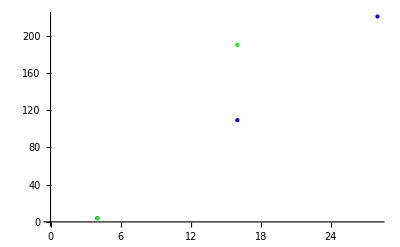

```mathematica
SetDirectory[NotebookDirectory[]];
ave[file_]:=Module[{dat},
dat=Transpose[Import[file][[]]][[8]];
Mean[dat]
]

dataip={{4,ave["he4ip.dat"]/ave["he4noip.dat"]},{16,320/8 ave["o16ip.dat"]/ave["o16noip.dat"]},{28,ave["nucmatip.dat"]/ave["nucmatnoip.dat"]}}
dataquad={{4,ave["he4quad.dat"]/ave["he4noip.dat"]},{16,336/8 ave["o16quad.dat"]/ave["o16noip.dat"]}}

ListPlot[{dataip,dataquad},PlotStyle->{{Blue},{Green}}]
```

```mathematica
NonlinearModelFit[data,a*x^2+b*x+c,{a,b,c},x]
```

FittedModel[-4.8761+1.24211 x+0.243295 x^2]

```mathematica
(A*(A-1)*(A-2)*(A-3))/8/(A(A-1)/2)//Expand
((A*(A-1)*(A-2)*(A-3))/8+(A(A-1)/2))/(A(A-1)/2)//FullSimplify//Expand
```

3/2-(5 A)/4+A^2/4

5/2-(5 A)/4+A^2/4

{{4.,1.5},{16.,46.5},{28.,163.5}}

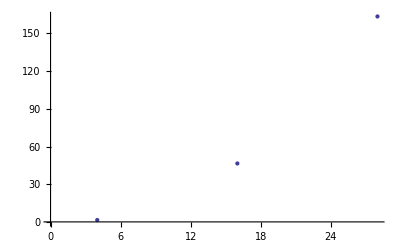

FittedModel[2.5-1.25 x+0.25 x^2]

```mathematica
test[A_]=((A*(A-1)*(A-2)*(A-3))/8+(A(A-1)/2))/(A(A-1)/2);
testdata={{4,test[4]},{16,test[16]},{28,test[28]}}//N
ListPlot[testdata]
NonlinearModelFit[testdata,a*x^2+b*x+c,{a,b,c},x]
```

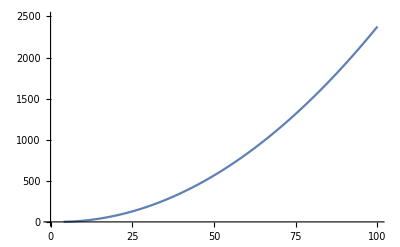

```mathematica
Plot[5/2-(5 A)/4+A^2/4,{A,4,100},PlotRange->{0,2500}]
```